```mathematica
$PlotTheme="Scientific"
```

Scientific

#### Formatting

```mathematica
Format[x1]=Subscript[a, 1];
Format[x2]=Subscript[a, 2];
Format[x3]=Subscript[a, 3];
Format[y1]=Subscript[a, t];
Format[y2]=Subscript[a, b];
Format[z]=Subscript[a, λ];
```

```mathematica
fontsize=20
```

20

#### For arrows

```mathematica
StyleEV[x_?Positive]:=Darker[ColorData[97,"ColorList"][[-5]],0.7];
StyleEV[x_?Negative]:=Darker[ColorData[97,"ColorList"][[-4]],0.7];
```

```mathematica
reverseArrow[x_?Positive]:=Identity
reverseArrow[x_?Negative]:= Reverse
```

```mathematica
ArrowsPM[ee_,sf_:0.02]:=N[ Flatten[Table[MapThread[{Arrowheads[Small],Style[Arrow[reverseArrow[#2] @ {First[ee[[i]]],First[ee[[i]]]+sf (#1)}],StyleEV[#2]]}&,{Part[ee[[i]],2],Part[ee[[i]],3]}],{i,Length[ee]}],{2,1}]];
```

### One-loop beta functions (3 variables)

```mathematica
vars = {x3,y1,z}
```

{a_3,a_t,a_λ}

Beta functions in Eq. 5

```mathematica
bb1L = {-7*x3^2, -8*x3*y1 + (9*y1^2)/2, -3*y1^2 + 6*y1*z + 12*z^2}
```

{-7 a_3^2,(9 a_t^2)/2-8 a_3 a_t,12 a_λ^2+6 a_λ a_t-3 a_t^2}

RHS of  Eq .10 (we removed a factor of x)

```mathematica
bb1LYZa = (bb1L[[{2,3}]]/vars[[1]]^2 -bb1L[[1]] vars[[{2,3}]]/vars[[1]]^3) /. y1->Y x3 /. z->Z x3//Simplify
```

{1/2 Y (9 Y-2),-3 Y^2+6 Y Z+Z (12 Z+7)}

RHS of  Eq 11 (we removed a factor of y)

```mathematica
bb1LXZa = (bb1L[[{1,3}]]/vars[[2]]^2 -bb1L[[2]] vars[[{1,3}]]/vars[[2]]^3) /. x3-> X y1 /. z->Z y1//FullSimplify
```

{X^2-(9 X)/2,(8 X+3/2) Z+12 Z^2-3}

Fixed points of two vector fields  (correspond to rays)

```mathematica
fpYZ = Solve[Thread[bb1LYZa==0],{Y,Z}]
```

{{Y→0,Z→-7/12},{Y→0,Z→0},{Y→2/9,Z→1/72 (-25-√689)},{Y→2/9,Z→1/72 (√689-25)}}

```mathematica
fpXZ = Solve[Thread[bb1LXZa==0],{X,Z}]
```

{{X→0,Z→1/16 (-1-√65)},{X→0,Z→1/16 (√65-1)},{X→9/2,Z→1/16 (-25-√689)},{X→9/2,Z→1/16 (√689-25)}}

### RG flow (Figure 1 & 3)

```mathematica
Clear[kruzhok]
```

```mathematica
kruzhok[text_,{x_,y_},fontsize_,r_]:={{White,Disk[{x,y},0.95r]},{Thickness[0.0035],Circle[{x,y},r]},Text[Style[text,FontSize->fontsize,FontFamily->fontfamily],{x,y}]};
```

```mathematica
kruzhok[text_,{x_,y_},fontsize_,r1_List]:={{White,Disk[{x,y},r1]},{Thickness[0.0035],Circle[{x,y},r1]},Text[Style[text,FontSize->fontsize,FontFamily->fontfamily],{x,y}]};
```

```mathematica
kruzhok[text_,{x_,y_},fontsize_,r1_Scaled]:={{White,Disk[{x,y},r1]},{Thickness[0.0035],Circle[{x,y},r1]},Text[Style[text,FontSize->fontsize,FontFamily->fontfamily],{x,y}]};
```

```mathematica
cm = 72/2.54
```

28.3465

```mathematica
fontsize=10.5
```

10.5

```mathematica
fontfamily = "TexMaths Symbols"
```

TexMaths Symbols

Figure 1

11

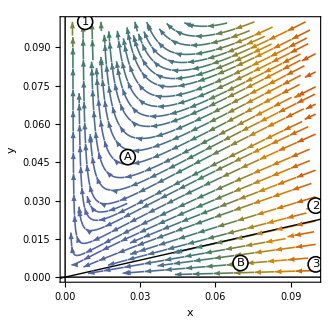

```mathematica
Fig1=StreamPlot[{-7 x^2,-8 x y+(9 y^2)/2},{x,0,0.1},{y,0,0.1},FrameLabel->{"x","y"},
Epilog->{InfiniteLine[{0,0},{0,1}],InfiniteLine[{0,0},{1,0}],InfiniteLine[{0,0},{1,2/9}],
kruzhok[Style["1",FontFamily->"TexMaths Roman"],{0.008,0.1},fontsize,0.003],kruzhok[Style["2",FontFamily->"TexMaths Roman"],{0.1,0.028},fontsize,0.003],kruzhok[Style["3",FontFamily->"TexMaths Roman"],{0.1,0.005},fontsize,0.003],kruzhok[Style["A",FontFamily->"TexMaths Roman"],{0.025,0.047},fontsize,0.003],kruzhok[Style["B",FontFamily->"TexMaths Roman"],{0.07,0.0055},fontsize,0.003]
},ImageSize->1.5imagesize,LabelStyle->{FontSize->1.1fontsize,FontFamily->fontfamily},Frame->True,PlotTheme->"Scientific",StreamStyle->{Arrowheads[0.025],Thickness[0.0035]}]
```

```mathematica
Export["Fig1.pdf",Fig1]
```

Fig1.pdf

Figure 3a (x=0)

```mathematica
fontsize=11.5
```

11.5

```mathematica
imagesize=5.5*1.43*cm;
```

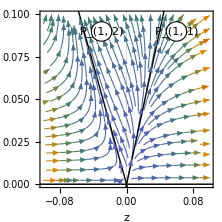

```mathematica
Fig3a=StreamPlot[Reverse @{9/2 y^2,6z(2z+y)-3y^2},{z,-0.1,0.1},{y,0,0.1},FrameLabel->{"z","y"},
Epilog->{InfiniteLine[{0,0},Reverse @ {0,1}],InfiniteLine[{0,0},Reverse @{1,(-1-Sqrt[65])/16}],InfiniteLine[{0,0},Reverse@ {1,(-1+Sqrt[65])/16}],
kruzhok["P_(1, 1)",{0.06,0.09},fontsize,Scaled[{0.059,0.055}]],kruzhok["P_(1, 2)",{-0.03,0.09},fontsize,Scaled[{0.059,0.055}]]},ImageSize->imagesize,LabelStyle->{FontSize->fontsize,FontFamily->fontfamily},Frame->True,PlotTheme->"Scientific",StreamStyle->{Arrowheads[0.025],Thickness[0.0035]}]
```

Figure 3b (y=2/9 x)

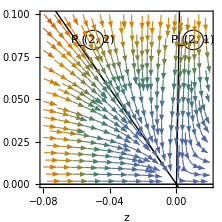

```mathematica
Fig3b=StreamPlot[Reverse @{-7x^2,6z(2z+2/9 x)-4/9 x^2},{z,-0.08,0.02},{x,0,0.1},FrameLabel->{Style["z",Italic],Style["x",Italic]},
Epilog->{InfiniteLine[{0,0},Reverse @{0,1}],InfiniteLine[{0,0},Reverse @{1,(-25-Sqrt[689])/72}],InfiniteLine[{0,0},Reverse @{1,(-25+Sqrt[689])/72}],
kruzhok["P_(2, 1)",Reverse @{0.085,0.01},fontsize,Scaled[{0.059,0.055}]],kruzhok["P_(2, 2)",Reverse @{0.085,-0.05},fontsize,Scaled[{0.059,0.055}]]},ImageSize->imagesize,LabelStyle->{FontSize->fontsize,FontFamily->fontfamily},Frame->True,StreamStyle->{Arrowheads[0.025],Thickness[0.0035]},PlotTheme->"Scientific",StreamStyle->{Arrowheads[0.025],Thickness[0.0035]}]
```

Figure 3c (y = 0)

28.3465

10

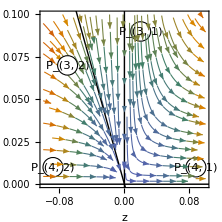

```mathematica
Fig3c=StreamPlot[Reverse @{-7x^2,12z^2},{z,-0.1,0.1},{x,0,0.1},FrameLabel->{"z","x"},
Epilog->{InfiniteLine[{0,0},{-7/12,1}],InfiniteLine[{0,0},{0,1}],InfiniteLine[{0,0},{1,0}],kruzhok["P_(4, 1)",Reverse@ {0.01,0.088},fontsize,Scaled[{0.059,0.055}]],
kruzhok["P_(3, 2)",{-0.07,0.07},fontsize,Scaled[{0.059,0.055}]],
kruzhok["P_(3, 1)",{0.02,0.09},fontsize,Scaled[{0.059,0.055}]],
kruzhok["P_(4, 2)",Reverse@ {0.01,-0.088},fontsize,Scaled[{0.059,0.055}]]
},ImageSize->imagesize,  LabelStyle->{FontSize->fontsize,FontFamily->fontfamily},Frame->True,PlotTheme->"Scientific",StreamStyle->{Arrowheads[0.025],Thickness[0.0035]}]
```

```mathematica
Export["Fig3a.pdf",Fig3a]
Export["Fig3b.pdf",Fig3b]
Export["Fig3c.pdf",Fig3c]
```

Fig3a.pdf

Fig3b.pdf

Fig3c.pdf

Fig3b.pdf

/home/bednya

### Figure 2

Here we investigate stability of fixed points (to add arrows)

```mathematica
omegaYZ=Transpose[D[bb1LYZa,#] & /@  {Y,Z}]
```

((9 Y)/2+1/2 (9 Y-2) | 0
6 Z-6 Y | 6 Y+24 Z+7)

```mathematica
omegaXZ=Transpose[D[bb1LXZa,#] & /@  {X,Z}]
```

(2 X-9/2 | 0
8 Z | 8 X+24 Z+3/2)

Eigenvectors and eigenvalues of the corresponding ω

```mathematica
eigvYZ=({{Z,Y} /. #,Normalize /@ Reverse /@ Eigenvectors[(omegaYZ /. #) ],Eigenvalues[(omegaYZ /. #)]})&/@ fpYZ ;
```

```mathematica
eigvXZ=({{Z,X} /. #,Normalize /@ Reverse /@ Eigenvectors[(omegaXZ /. #) ],Eigenvalues[(omegaXZ /. #)]})&/@ fpXZ ;
```

```mathematica
pppPYZ = (Last/@ Last/@ First/@ Last /@ArrowsPM[eigvYZ,+0.03]);
pppMYZ = (Last/@ Last/@ First/@ Last /@ArrowsPM[eigvYZ,-0.03]);
```

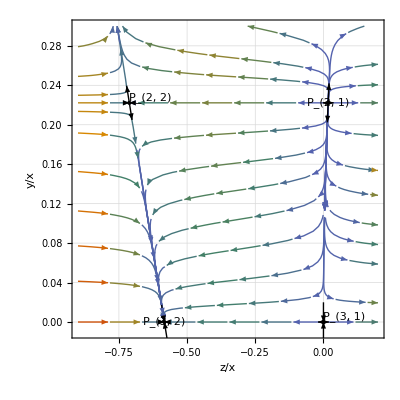

```mathematica
spYZ=StreamPlot[Reverse[ bb1LYZa],{Z,-0.9,0.2},{Y,-0.01,0.3},
StreamPoints->{Join[{
{-0.6,0},
{-0.8,0.15},
{-0.8,0.11},
{-0.8,0.19},
{-0.8,0.04},
{-0.8,0.075},
{-0.85,0.25},
{-0.88,0.28},
{-0.8,2/9},
{-0.4,0.04},
{-0.4,0.07},
{-0.4,0.1},
{-0.4,0.19},
{-0.4,0.13},
{-0.4,0.25},
{-0.4,0.27},

{-0.2,0.02},

{0.15,0.02},
{0.15,0.06},
{0.15,0.08},
{0.15,0.10},
{0.15,0.13},
{0.15,0.155},
{0.15,0.19},
{0.15,0.24},
{0.15,0.26},
{0.15,0.30}
		},pppPYZ,pppMYZ],{0.2,0.02},Scaled[0.8]},
Epilog->Join[ArrowsPM[eigvYZ,+0.02],ArrowsPM[eigvYZ,-0.02],(Point[{Z,Y}]/. fpYZ),
{Text[Style["P_(3, 1)",FontFamily->"Times",Italic],{0,0},{-1.4,-1.4}],
Text[Style["P_(3, 2)",FontFamily->"Times",Italic],{-7/12,0},{2,-1.4}],
Text[Style["P_(2, 2)",FontFamily->"Times",Italic],{-1/72 (25+Sqrt[689]),2/9},{-1.4,-1.4}],
Text[Style["P_(2, 1)",FontFamily->"Times",Italic],{-1/72 (25-Sqrt[689]),2/9},{2,-1.4}]}
],StreamScale->{0.10,Scaled[0.2],Scaled[0.4]},BaseStyle->14,FrameLabel->{Style["z/x",Italic],Style["y/x",Italic]},PlotLegends->Automatic,PerformanceGoal->"Quality",Frame->True,GridLines->{Automatic,Automatic},WorkingPrecision->100]
```

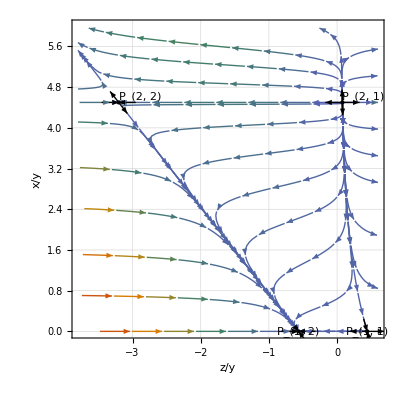

```mathematica
spXZ=StreamPlot[Reverse[bb1LXZa],{Z,-3.8,0.6},{X,-0.01,6},
StreamPoints->{
{
{-3.5,5.1}
,{-3.5,4.8}
,{-3.5,4.5}
,{-3.5,4.1}
,{-3.5,3.2}
,{-3.5,2.4}
,{-3.5,1.5}
,{-3.5,0.7}

,{-3,4.15236676782}
,{-2,4}
,{-2,4.5}
,{-1,2}
,{-1,2.8}
,{-1,3.5}

,{-1,5.5}

,{-1,0}
,{-0.4,1.4}
,{-0.4,0.4}
,{-0.4,5.1}
,{0,0}
,{0,5.7}
,{0.4,0.01}
,{0.4,1}
,{0.4,2}
,{0.4,3}
,{0.4,3.5}
,{0.4,4}
,{0.4,4.5}
,{0.4,5}
,{0.4,5.5}
}
,
{0.2,0.02},Scaled[0.8]},
Epilog->Join[ArrowsPM[eigvXZ,+0.25],ArrowsPM[eigvXZ,-0.25],{PointSize[Small],Point[{Z,X}]}/. fpXZ,{Text[Style["P_(1, 2)",FontFamily->"Times",Italic],{-1/16 (1+Sqrt[65]),0},{2,-1.4}],
Text[Style["P_(1, 1)",FontFamily->"Times",Italic],{-1/16 (1-Sqrt[65]),0},{2,-1.4}],
Text[Style["P_(2, 2)",FontFamily->"Times",Italic],{-1/16 (25+Sqrt[689]),9/2},{-1.4,-1.4}],
Text[Style["P_(2, 1)",FontFamily->"Times",Italic],{-1/16 (25-Sqrt[689]),9/2},{-1.4,-1.4}]}],BaseStyle->14,Frame->True,GridLines->{Automatic,Automatic},StreamScale->{0.10,Scaled[0.2],Scaled[0.4]},

(*,BaseStyle->{FontFamily->"Times",14},FrameStyle->{FontFamily->"Times"},*)FrameLabel->{Style["z/y",Italic],Style["x/y",Italic]},PerformanceGoal->"Quality",Frame->True,GridLines->{Automatic,Automatic},WorkingPrecision->100]
```

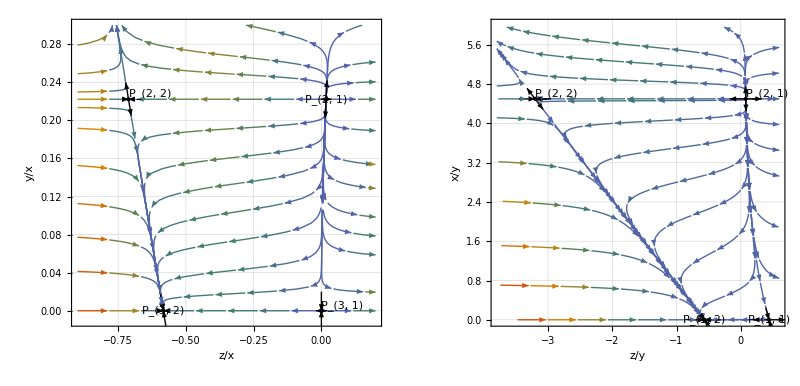

```mathematica
GraphicsRow[{spYZ,spXZ},ImageSize->Full]
```

### Figure 4

```mathematica
varsX = {x1,x2,x3,y1,y2}
```

{a_1,a_2,a_3,a_t,a_b}

Beta functions in Eq. 19  (w/o last eq)

```mathematica
bb1LX ={(41*x1^2)/10,(-19*x2^2)/6,-7*x3^2,(-17*x1*y1-45*x2*y1-160*x3*y1+90*y1^2+30*y1*y2)/20,(-(x1*y2)-9*x2*y2-32*x3*y2+6*y1*y2+18*y2^2)/4}//Expand;
```

```mathematica
BlowupsSM1LX = Table[Simplify[Delete[bb1LX,i]/varsX[[i]]^2 - Delete[varsX,i]/varsX[[i]]^3 bb1LX[[i]] /. (Thread[Delete[varsX,i]-> ((ratio/@ (Delete[varsX,i]/varsX[[i]])) *varsX[[i]])])] ,{i,Length[varsX]}]
```

(-1/30 ratio(a_2/a_1) (95 ratio(a_2/a_1)+123) | -1/10 ratio(a_3/a_1) (70 ratio(a_3/a_1)+41) | 1/20 ratio(a_t/a_1) (30 ratio(a_b/a_1)+90 ratio(a_t/a_1)-45 ratio(a_2/a_1)-160 ratio(a_3/a_1)-99) | 1/20 ratio(a_b/a_1) (90 ratio(a_b/a_1)+30 ratio(a_t/a_1)-45 ratio(a_2/a_1)-160 ratio(a_3/a_1)-87)
1/30 ratio(a_1/a_2) (123 ratio(a_1/a_2)+95) | 19/6 ratio(a_3/a_2)-7 (ratio(a_3/a_2))^2 | 1/60 ratio(a_t/a_2) (90 ratio(a_b/a_2)+270 ratio(a_t/a_2)-51 ratio(a_1/a_2)-480 ratio(a_3/a_2)+55) | 1/12 ratio(a_b/a_2) (54 ratio(a_b/a_2)+18 ratio(a_t/a_2)-3 ratio(a_1/a_2)-96 ratio(a_3/a_2)+11)
1/10 ratio(a_1/a_3) (41 ratio(a_1/a_3)+70) | 7 ratio(a_2/a_3)-19/6 (ratio(a_2/a_3))^2 | 1/20 ratio(a_t/a_3) (5 (6 ratio(a_b/a_3)+18 ratio(a_t/a_3)-9 ratio(a_2/a_3)-4)-17 ratio(a_1/a_3)) | 1/4 ratio(a_b/a_3) (18 ratio(a_b/a_3)+6 ratio(a_t/a_3)-ratio(a_1/a_3)-9 ratio(a_2/a_3)-4)
1/20 ratio(a_1/a_t) (5 (-6 ratio(a_b/a_t)+9 ratio(a_2/a_t)+32 ratio(a_3/a_t)-18)+99 ratio(a_1/a_t)) | -1/60 ratio(a_2/a_t) (90 ratio(a_b/a_t)-51 ratio(a_1/a_t)+55 ratio(a_2/a_t)-480 ratio(a_3/a_t)+270) | 1/20 ratio(a_3/a_t) (5 (-6 ratio(a_b/a_t)+9 ratio(a_2/a_t)+4 ratio(a_3/a_t)-18)+17 ratio(a_1/a_t)) | 3/5 ratio(a_b/a_t) (5 ratio(a_b/a_t)+ratio(a_1/a_t)-5)
1/20 ratio(a_1/a_b) (5 (-6 ratio(a_t/a_b)+9 ratio(a_2/a_b)+32 ratio(a_3/a_b)-18)+87 ratio(a_1/a_b)) | -1/12 ratio(a_2/a_b) (18 ratio(a_t/a_b)-3 ratio(a_1/a_b)+11 ratio(a_2/a_b)-96 ratio(a_3/a_b)+54) | 1/4 ratio(a_3/a_b) (-6 ratio(a_t/a_b)+ratio(a_1/a_b)+9 ratio(a_2/a_b)+4 ratio(a_3/a_b)-18) | 3/5 ratio(a_t/a_b) (5 ratio(a_t/a_b)-ratio(a_1/a_b)-5))

```mathematica
YtYbField=BlowupsSM1LX[[3]][[{3,4}]] /. ratio[y1/x3]->Yt /. ratio[y2/x3]->Yb;
```

#### a_1=a_2=0

```mathematica
YtYbFieldA1A2zero=YtYbField/. x2->0 /. x1->0 /. ratio[0]->0
```

{1/4 Yt (6 Yb+18 Yt-4),1/4 Yb (18 Yb+6 Yt-4)}

```mathematica
YtYbFieldA1A2zeroFP  = Solve[Thread[YtYbFieldA1A2zero==0]]
```

{{Yb→0,Yt→2/9},{Yb→1/6,Yt→1/6},{Yb→2/9,Yt→0},{Yb→0,Yt→0}}

```mathematica
YtYbFieldA1A2zeroOmega  = Transpose[D[YtYbFieldA1A2zero,#] & /@  {Yt,Yb}]
```

(1/4 (6 Yb+18 Yt-4)+(9 Yt)/2 | (3 Yt)/2
(3 Yb)/2 | 1/4 (18 Yb+6 Yt-4)+(9 Yb)/2)

```mathematica
YtYbFieldA1A2zeroEigenV=({{Yt,Yb} /. #,Normalize /@ Eigenvectors[(YtYbFieldA1A2zeroOmega /. #) ],Eigenvalues[(YtYbFieldA1A2zeroOmega /. #)]})&/@ YtYbFieldA1A2zeroFP
```

({2/9,0} | (1 | 0
-1/(√26) | 5/(√26)) | {1,-2/3}
{1/6,1/6} | (1/(√2) | 1/(√2)
-1/(√2) | 1/(√2)) | {1,1/2}
{0,2/9} | (0 | 1
-5/(√26) | 1/(√26)) | {1,-2/3}
{0,0} | (0 | 1
1 | 0) | {-1,-1})

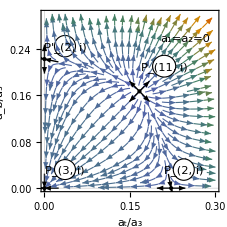

```mathematica
Fig4a=StreamPlot[YtYbFieldA1A2zero,{Yt,0,0.3},{Yb,0,0.3
},FrameLabel->{"a_t/a_3","a_b/a_3"},Epilog->{
Inset[Style[Framed["a_1=a_2=0",RoundingRadius->10,FrameStyle->{Thin}],FontSize->fontsize,FontFamily->fontfamily,Background->White],Scaled[{0.81,0.85}]],
kruzhok["P_(3, i)",{0.036,0.032},fontsize,Scaled[{0.059,0.055}]],
kruzhok["P_(2, i)",{1.1 2/9,0.032},fontsize,Scaled[{0.059,0.059}]],
kruzhok["P'_(2, i)",{0.036,1.1 2/9},fontsize,Scaled[{0.059,0.059}]],
kruzhok["P_(11, i)",{0.21,0.21},fontsize,Scaled[{0.065,0.06}]],
ArrowsPM[YtYbFieldA1A2zeroEigenV,0.025],
ArrowsPM[YtYbFieldA1A2zeroEigenV,-0.025],
(Point[{Yt,Yb}]/. YtYbFieldA1A2zeroFP)
(*kruzhok["0",{0,0},18,0.015],kruzhok["2'",{0,2/9},18,0.015],kruzhok["2^+",{1/6,1/6},18,0.015],kruzhok["2",{2/9,0},18,0.015]*)},ImageSize->1.025imagesize,LabelStyle->{FontSize->fontsize,FontFamily->fontfamily},Frame->True,PlotTheme->"Scientific",StreamStyle->{Arrowheads[0.025],Thickness[0.0035]}]
```

```mathematica
Export["Fig4a.pdf",Fig4a]
```

Fig4a.pdf

#### a_1=0, a_2=42/19 a_3

```mathematica
YtYbFieldA2nonzero=YtYbField /. x1->0 /. x2->42/19 x3 /. ratio[x_]:>x
```

{1/4 Yt (6 Yb+18 Yt-454/19),1/4 Yb (18 Yb+6 Yt-454/19)}

```mathematica
YtYbFieldA2nonzeroFP  = Solve[Thread[YtYbFieldA2nonzero==0]]
```

{{Yb→0,Yt→227/171},{Yb→227/228,Yt→227/228},{Yb→227/171,Yt→0},{Yb→0,Yt→0}}

```mathematica
YtYbFieldA2nonzeroOmega  = Transpose[D[YtYbFieldA2nonzero,#] & /@  {Yt,Yb}]
```

(1/4 (6 Yb+18 Yt-454/19)+(9 Yt)/2 | (3 Yt)/2
(3 Yb)/2 | 1/4 (18 Yb+6 Yt-454/19)+(9 Yb)/2)

```mathematica
YtYbFieldA2nonzeroEigenV=({{Yt,Yb} /. #,Normalize /@ Eigenvectors[(YtYbFieldA2nonzeroOmega /. #) ],Eigenvalues[(YtYbFieldA2nonzeroOmega /. #)]})&/@ YtYbFieldA2nonzeroFP ;
```

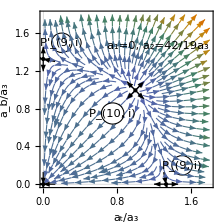

```mathematica
Fig4b=StreamPlot[YtYbFieldA2nonzero,{Yt,0,1.8},{Yb,0,1.8},FrameLabel->{"a_t/a_3","a_b/a_3"},
Epilog->{
Inset[Style[Framed["a_1=0, a_2=42/19a_3",RoundingRadius->10,FrameStyle->{Thin}],Italic,FontSize->fontsize,FontFamily->fontfamily,Background->White],Scaled[{0.68,0.80}]],
ArrowsPM[YtYbFieldA2nonzeroEigenV,0.13],
ArrowsPM[YtYbFieldA2nonzeroEigenV,-0.13],
(Point[{Yt,Yb}]/. YtYbFieldA2nonzeroFP),
kruzhok["P_(9, i)",{1.5,0.2},fontsize,Scaled[{0.059,0.055}]],
kruzhok["P'_(9, i)",{0.2,1.5},fontsize,Scaled[{0.059,0.055}]],
kruzhok["P_(10, i)",{0.75,0.75},fontsize,Scaled[{0.065,0.06}]]
(*kruzhok["0",{0,0},18,0.015],kruzhok["2'",{0,2/9},18,0.015],kruzhok["2^+",{1/6,1/6},18,0.015],kruzhok["2",{2/9,0},18,0.015]*)},ImageSize->imagesize,LabelStyle->{FontSize->fontsize,FontFamily->fontfamily},Frame->True,PlotTheme->"Scientific",StreamStyle->{Arrowheads[0.025],Thickness[0.0035]}]
```

#### a_2=a_3=0

```mathematica
YtYbFieldA1=BlowupsSM1LX[[1]][[{3,4}]] /. ratio[y1/x1]->Yt /. ratio[y2/x1]->Yb /. x2->0 /. x3->0 /. ratio[0]->0
```

{1/20 Yt (30 Yb+90 Yt-99),1/20 Yb (90 Yb+30 Yt-87)}

```mathematica
YtYbFieldA1FP  = Solve[Thread[YtYbFieldA1==0]]
```

{{Yb→0,Yt→11/10},{Yb→27/40,Yt→7/8},{Yb→29/30,Yt→0},{Yb→0,Yt→0}}

```mathematica
YtYbFieldA1FPOmega  = Transpose[D[YtYbFieldA1,#] & /@  {Yt,Yb}]
```

(1/20 (30 Yb+90 Yt-99)+(9 Yt)/2 | (3 Yt)/2
(3 Yb)/2 | 1/20 (90 Yb+30 Yt-87)+(9 Yb)/2)

```mathematica
YtYbFieldA1EigenV=({{Yt,Yb} /. #,Normalize /@ Eigenvectors[(YtYbFieldA1FPOmega /. #) ],Eigenvalues[(YtYbFieldA1FPOmega /. #)]})&/@ YtYbFieldA1FP ;
```

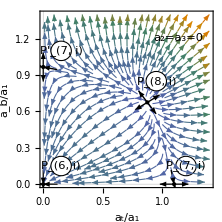

```mathematica
Fig4c=StreamPlot[YtYbFieldA1,{Yt,0,1.4},{Yb,0,1.4},FrameLabel->{"a_t/a_1","a_b/a_1"},RotateLabel->True,
(* StreamPoints->{{
{0.4,0}
,{1.4,0}
,{0,0.4}
,{0,1.4}

,{0.1,0.9475}
,{0.14,0.78}
,{0.2,0.6}
,{0.4,0.4}
,{0.4,0.56}
,{0.4,1},
,{0.6,0.4}
,{0.7,0.3}
,{0.9,0.23}
,{0.94,0.5553858}
,{0.94,0.1}
},
Automatic,Scaled[0.7]},*)
Epilog->{
Inset[Style[Framed["a_2=a_3=0",RoundingRadius->10,FrameStyle->{Thin}],FontSize->fontsize,FontFamily->fontfamily,Background->White],Scaled[{0.80,0.85}]],
ArrowsPM[YtYbFieldA1EigenV,0.12],
ArrowsPM[YtYbFieldA1EigenV,-0.12],
(Point[{Yt,Yb}]/. YtYbFieldA1FP),
kruzhok["P_(6, i)",{0.15,0.15},fontsize,Scaled[{0.059,0.055}]],
kruzhok["P_(7, i)",{1.2,0.15},fontsize,Scaled[{0.059,0.055}]],
kruzhok["P'_(7, i)",{0.15,1.1},fontsize,Scaled[{0.059,0.055}]],
kruzhok["P_(8, i)",{0.95,0.85},fontsize,Scaled[{0.059,0.055}]]
}
,ImageSize->imagesize,LabelStyle->{FontSize->fontsize,FontFamily->fontfamily},Frame->True,PlotTheme->"Scientific",StreamStyle->{Arrowheads[0.025],Thickness[0.0035]}]
```

```mathematica
Export["Fig4a.pdf",Fig4a]
Export["Fig4b.pdf",Fig4b]
Export["Fig4c.pdf",Fig4c]
```

Fig4a.pdf

Fig4b.pdf

Fig4c.pdf

### Figure 6

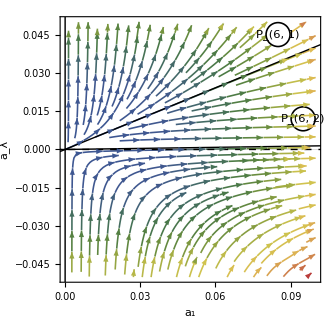

```mathematica
Fig6=StreamPlot[{(41 x1^2)/10,(27 x1^2)/400-(9 x1 z)/10+12 z^2},{x1,0,0.1},{z,-0.05,0.05},FrameLabel->{"a_1","a_λ"},
Epilog->{InfiniteLine[{0,0},{0,1}],InfiniteLine[{0,0},{1,1/120 (25-4 √34)}],InfiniteLine[{0,0},{1,1/120 (25+4 √34)}],{Dashed,InfiniteLine[{0,0},{1,0}]},kruzhok["P_(6, 1)",{0.085,0.045},fontsize,Scaled[{0.046,0.045}]],kruzhok["P_(6, 2)",{0.095,0.012},fontsize,Scaled[{0.046,0.045}]]} ,ImageSize->1.5imagesize,LabelStyle->{FontSize->fontsize,FontFamily->fontfamily},Frame->True,PlotTheme->"Scientific",StreamStyle->{Arrowheads[0.025],Thickness[0.0035]},StreamColorFunction->"DarkRainbow"]
```

```mathematica
Export["Fig6.pdf",Fig6]
```

Fig6.pdf